### Start choosing the example:

```mathematica
t=6;
beta=0;
A=0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{10,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.023746,Null}

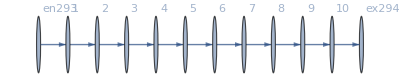

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j295→80.,j296→80.,j297→80.,j298→80.,j299→80.,j300→80.,j301→80.,j302→80.,j303→80.,j304→80.,j305→80.,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80.,jt319→80.,jt320→0.,jt321→80.,jt322→0.,jt323→80.,jt324→0.,jt325→80.,jt326→0.,jt327→80.,jt328→0.,jt329→80.,jt330→0.,jt331→80.,jt332→0.,jt333→80.,jt334→0.,jt335→80.,jt336→0.,u337→735.,u338→655.,u339→575.,u340→495.,u341→415.,u342→335.,u343→255.,u344→175.,u345→95.,u346→15.,u347→735.,u348→655.,u349→575.,u350→495.,u351→415.,u352→335.,u353→255.,u354→175.,u355→95.,u356→15.,u357→15.,u358→735.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→38.2376,u338→35.6556,u339→33.0737,u340→30.4917,u341→27.9098,u342→25.3278,u343→22.7459,u344→20.1639,u345→17.582,u346→15.,u347→38.2376,u348→35.6556,u349→33.0737,u350→30.4917,u351→27.9098,u352→25.3278,u353→22.7459,u354→20.1639,u355→17.582,u356→15.,u357→15.,u358→38.2376|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→43.4521,u338→40.2907,u339→37.1294,u340→33.968,u341→30.8067,u342→27.6454,u343→24.484,u344→21.3227,u345→18.1613,u346→15.,u347→43.4521,u348→40.2907,u349→37.1294,u350→33.968,u351→30.8067,u352→27.6454,u353→24.484,u354→21.3227,u355→18.1613,u356→15.,u357→15.,u358→43.4521|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→60.215,u338→55.1911,u339→50.1672,u340→45.1433,u341→40.1195,u342→35.0956,u343→30.0717,u344→25.0478,u345→20.0239,u346→15.,u347→60.215,u348→55.1911,u349→50.1672,u350→45.1433,u351→40.1195,u352→35.0956,u353→30.0717,u354→25.0478,u355→20.0239,u356→15.,u357→15.,u358→60.215|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.55795×10^-13,ComplexInfinity]

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→735.,u338→655.,u339→575.,u340→495.,u341→415.,u342→335.,u343→255.,u344→175.,u345→95.,u346→15.,u347→735.,u348→655.,u349→575.,u350→495.,u351→415.,u352→335.,u353→255.,u354→175.,u355→95.,u356→15.,u357→15.,u358→735.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.29622×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.29622×10^-16

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→3290.15,u338→2926.25,u339→2562.34,u340→2198.43,u341→1834.53,u342→1470.62,u343→1106.72,u344→742.811,u345→378.906,u346→15.,u347→3290.15,u348→2926.25,u349→2562.34,u350→2198.43,u351→1834.53,u352→1470.62,u353→1106.72,u354→742.811,u355→378.906,u356→15.,u357→15.,u358→3290.15|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→2.6104×10^6,u338→2.32036×10^6,u339→2.03032×10^6,u340→1.74027×10^6,u341→1.45023×10^6,u342→1.16019×10^6,u343→870144.,u344→580101.,u345→290058.,u346→15.,u347→2.6104×10^6,u348→2.32036×10^6,u349→2.03032×10^6,u350→1.74027×10^6,u351→1.45023×10^6,u352→1.16019×10^6,u353→870144.,u354→580101.,u355→290058.,u356→15.,u357→15.,u358→2.6104×10^6|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.28307×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.28307×10^-16

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→1.40355×10^8,u338→1.2476×10^8,u339→1.09165×10^8,u340→9.357×10^7,u341→7.7975×10^7,u342→6.238×10^7,u343→4.6785×10^7,u344→3.119×10^7,u345→1.5595×10^7,u346→15.,u347→1.40355×10^8,u348→1.2476×10^8,u349→1.09165×10^8,u350→9.357×10^7,u351→7.7975×10^7,u352→6.238×10^7,u353→4.6785×10^7,u354→3.119×10^7,u355→1.5595×10^7,u356→15.,u357→15.,u358→1.40355×10^8|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.9109×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.9109×10^-16

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→5.04333×10^19,u338→4.48296×10^19,u339→3.92259×10^19,u340→3.36222×10^19,u341→2.80185×10^19,u342→2.24148×10^19,u343→1.68111×10^19,u344→1.12074×10^19,u345→5.6037×10^18,u346→15.,u347→5.04333×10^19,u348→4.48296×10^19,u349→3.92259×10^19,u350→3.36222×10^19,u351→2.80185×10^19,u352→2.24148×10^19,u353→1.68111×10^19,u354→1.12074×10^19,u355→5.6037×10^18,u356→15.,u357→15.,u358→5.04333×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.07956×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.07956×10^-16

<|j295→80,j296→80,j297→80,j298→80,j299→80,j300→80,j301→80,j302→80,j303→80,j304→80,j305→80,j306→0.,j307→0.,j308→0.,j309→0.,j310→0.,j311→0.,j312→0.,j313→0.,j314→0.,j315→0.,j316→0.,jt317→0.,jt318→80,jt319→80,jt320→0.,jt321→80,jt322→0.,jt323→80,jt324→0.,jt325→80,jt326→0.,jt327→80,jt328→0.,jt329→80,jt330→0.,jt331→80,jt332→0.,jt333→80,jt334→0.,jt335→80,jt336→0.,u337→1.98441×10^107,u338→1.76392×10^107,u339→1.54343×10^107,u340→1.32294×10^107,u341→1.10245×10^107,u342→8.81959×10^106,u343→6.61469×10^106,u344→4.4098×10^106,u345→2.2049×10^106,u346→15.,u347→1.98441×10^107,u348→1.76392×10^107,u349→1.54343×10^107,u350→1.32294×10^107,u351→1.10245×10^107,u352→8.81959×10^106,u353→6.61469×10^106,u354→4.4098×10^106,u355→2.2049×10^106,u356→15.,u357→15.,u358→1.98441×10^107|>